{1,4,16,19,31,34,1,4,16,19,31,34,1}

{1,5,25,35,40,20,10,5,25,35,40,20,10}

{1,4,5,10,16,19,20,25,31,34,35,40}

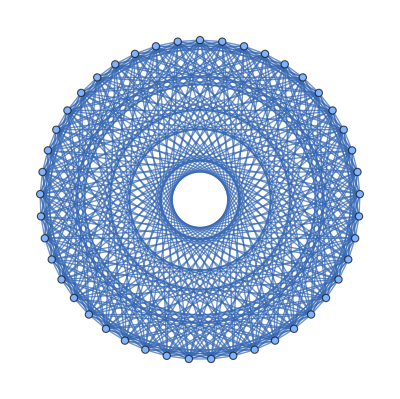

{{1,2,6}}

{{1,4,7,10,13,16,19,22,25,28,31,34,37,40,43}}

```mathematica
s=45;
li4=Table[Mod[4^i,s],{i,0,12}]
li3=Table[Mod[5^i,s],{i,0,12}]
li=Union[li4,li3]
g=CirculantGraph[s,li]
FindClique[g]
FindIndependentVertexSet[g]
```

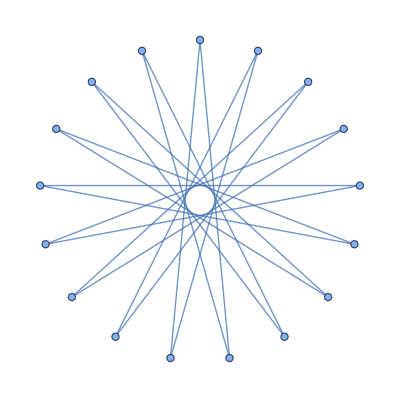

```mathematica
g8=CirculantGraph[s,{8}]
```